The presentation begins with convincing everyone that

α=tan^-1 sinβ/(e+cosβ)

But we want to know β in terms of α, so we have to solve this equation. Ok, here we go:

(e+cosβ)tanα=sinβ

Then we let w=sinβ:

(e+√(1-w^2))tanα=w

This is getting to be a quadratic equation for w. Isolate the square root:

√(1-w^2)=w/tanα-e

Then square and FOIL, and it is now obviously a quadratic equation in w:

1-w^2=w^2/(tan^2 α)-2 ew/tanα+e^2

or

0=w^2(1+1/(tan^2 α)))-2 ew/tanα+e^2-1

Then we used the quadratic formula.

w=((2e)/tanα±√(((2e)/tanα)^2+4(1+1/(tan^2 α))(1-e^2)))/(2(1+1/(tan^2 α)))

The + sign is relevant, at least for the part of the circle where α and β are both positive and increasing. Once cosα goes negative, I think we want the - sign. See below.

Cancel all the 2’s. Put back in that w=sinβ.

sinβ=(e/tanα+√((e/tanα)^2+(1+1/(tan^2 α))(1-e^2)))/(1+1/(tan^2 α))

Use that 1+1/(tan^2 α)=1+(cos^2 α)/(sin^2 α)=(sin^2 α + cos^2 α)/(sin^2 α)=1/(sin^2 α). Multiply numerator and denominator through by sin^2 α.

sinβ=(e/tanα+√((e/tanα)^2+1/(sin^2 α)(1-e^2)))/(1/(sin^2 α))=(e/tanα+√((e/tanα)^2+1/(sin^2 α)(1-e^2)))sin^2 α=(e cosα+√((e cosα)^2+(1-e^2)))sinα

Or

β=sin^-1[(e cosα+√((e cosα)^2+1-e^2))sinα]

Let’s look at this function with e=0. It simplifies to:

β=sin^-1[sinα]

This causes trouble! It doesn’t simplify to β=α! If it did, this would be a straight line:

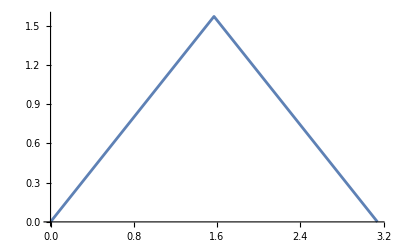

```mathematica
Plot[ArcSin[Sin[α]],{α,0, Pi}]
```

Even with e!=0, there is going to be a value of α for which (e cosα+√((e cosα)^2+1-e^2))sinα reaches 1 and starts decreasing. From that value on, we need β to keep increasing. Where does this function reach 1? It happens when α=tan^-1(1/e).

So we need to fix our formula to work properly beyond α=tan^-1(1/e). Here is how to do that:

```mathematica
e=0.2;
```

```mathematica
beta[α_]:=ArcSin[(e Cos[α]+Sqrt[(e Cos[α])^2+1-e^2])Sin[α]]
```

```mathematica
betaFixed[α_]:=If[α<ArcTan[1/e],beta[α],Pi-beta[α]]
```

```mathematica
q[α_]:=betaFixed[α]-α
```

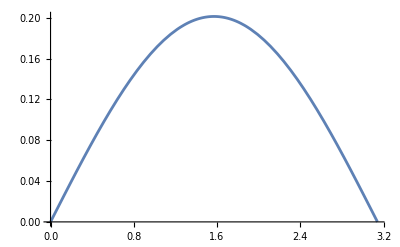

```mathematica
Plot[q[α],{α,0,Pi}]
```

As you can see this thing peaks out at π/2. Let’s re-plot the function in degrees for the actual value of e:

```mathematica
e=0.0334;
```

```mathematica
qInDegrees[α_]:=180 betaFixed[Pi α/180]/Pi-α
```

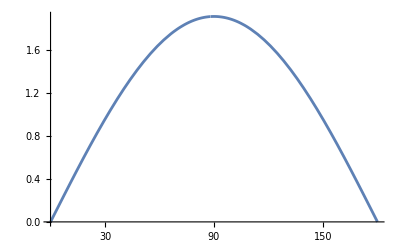

```mathematica
Plot[qInDegrees[α],{α,0,180}, Ticks->{{30, 60, 90, 120, 150, 180},Automatic}]
```